# Лабораторная работа №6

1205-010303D, Белов А.А.

```mathematica
SetOptions[Plot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
SetOptions[ParametricPlot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
SetOptions[ListPlot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
```

# Задание 1

Функция плотности

```mathematica
ρ[h_]:=QuantityMagnitude[StandardAtmosphereData[Quantity[h,"Meters"],"Density",Method->"USStandardAtmosphere"]];
```

## Уравнения движения c g = const

```mathematica
params={Subscript[c, d]->1.3,Subscript[c, L]->0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0};
```

```mathematica
q={V[t],r[t],θ[t],s[t]};
```

```mathematica
eqWithg={
V'[t]==-g Sin[θ[t]]-Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
V[t] θ'[t]==g(V[t]^2/(r[t] g)-1)Cos[θ[t]]+Subscript[c, L] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
s'[t]==V[t]/r[t] Cos[θ[t]] Rz, 
r'[t]==V[t] Sin[θ[t]]
};
```

```mathematica
paramsWithg={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9}
nu={V[0]==√(μ/(Rz+h0)),θ[0]==0,r[0]==Rz+h0,s[0]==0};
```

{c_d→1.3,c_L→0.,S→3.80133,m→3000.,g→9.807,Rz→6.371×10^6,h0→100000.,μ→3.986×10^14}

```mathematica
tk=1000;
```

```mathematica
solWithg=NDSolve[
{
eqWithg,nu,
WhenEvent[r[t]<=Rz//.paramsWithg,"StopIntegration"]
}//.paramsWithg,q,{t,0,tk}]

tkWithg=solWithg[[1,1,2,0,1,1,2]]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 770.387 and t = 770.401.

{{V[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}}

770.401

```mathematica
r[t]-Rz/.solWithg/.paramsWithg/.t->tkWithg
```

{9.03383×10^-8}

## Уравнения движения с меняющейся высотой

g =μ/(Rz+h0)^2

```mathematica
eqWithoutg={
V'[t]==-μ/(r[t])^2 Sin[θ[t]]-Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
V[t] θ'[t]==μ/(r[t])^2(V[t]^2/(r[t] μ/(r[t])^2)-1)Cos[θ[t]]+Subscript[c, L] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
s'[t]==V[t]/r[t] Cos[θ[t]] Rz, 
r'[t]==V[t] Sin[θ[t]]
};
```

```mathematica
paramsWithoutg={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9}
nu={V[0]==√(μ/(Rz+h0)),θ[0]==0,r[0]==Rz+h0,s[0]==0};
```

{c_d→1.3,c_L→0.,S→3.80133,m→3000.,Rz→6.371×10^6,h0→100000.,μ→3.986×10^14}

```mathematica
tk=2000;
solWithoutg=NDSolve[
{
eqWithoutg,nu,
WhenEvent[r[t]<=Rz//.paramsWithoutg,"StopIntegration"]
}//.paramsWithoutg,q,{t,0,tk}]

tkWithoutg=solWithoutg[[1,1,2,0,1,1,2]]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1566.3 and t = 1566.32.

{{V[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}}

1566.31

## Сравнение результатов

Дальность при g = const

```mathematica
0.001*s[t]/.paramsWithg/.solWithg/.t->tkWithg
```

{4543.22}

Дальность при g = μ/r[t]^2

```mathematica
0.001*s[t]/.paramsWithoutg/.solWithoutg/.t->tkWithoutg
```

{10640.2}

Таким образом, дальность полета спускаемого аппарата при учете и без учета изменения ускорения свободного падения от высоты полета отличается на 6096.9 км.

# Задание 2. Перегрузка

Функция плотности интерполяционная

```mathematica
ρ[h_]:=Interpolation[
{#,
QuantityMagnitude[StandardAtmosphereData[Quantity[#,"Meters"],"Density",Method->"USStandardAtmosphere"]]
}&/@Range[-1000,105000,2000]][h]
```

Уравнения движения

```mathematica
eq={
V'[t]==-g Sin[θ[t]]-Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
V[t] θ'[t]==g(V[t]^2/(r[t] g)-1)Cos[θ[t]]+Subscript[c, L] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
s'[t]==V[t]/r[t] Cos[θ[t]] Rz, 
r'[t]==V[t] Sin[θ[t]]
};
```

Функция вычисления перегрузки - принимает начальный угол входа в атмосферу, возвращает максимальное значение перегрузки при данном угле

```mathematica
peregruz[θ0_?NumberQ]:=Module[{params,nu,neq,tk,sol},
params={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9};
nu={V[0]==√(μ/(Rz+h0)),θ[0]==θ0,r[0]==Rz+h0,s[0]==0};
neq=eq/.params;
sol=NDSolve[{eq,nu,
WhenEvent[r[t]<=Rz//.params,"StopIntegration",DetectionMethod->"Sign"]}//.params,
q,{t,0,1000}];
tk=sol[[1,1,2,0,1,1,2]];
MaxValue[{(Norm[{Subscript[c, d],Subscript[c, L]}S(ρ[r[t]-Rz] V[t]^2)/2]/(g m)//.sol//.params)[[1]],t<tk,t>0},t]
];
```

График зависимости максимальной перегрузки от угла от минус 15 ° до 0 °

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 167.703 and t = 169.937.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 173.124 and t = 175.759.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 177.575 and t = 179.993.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

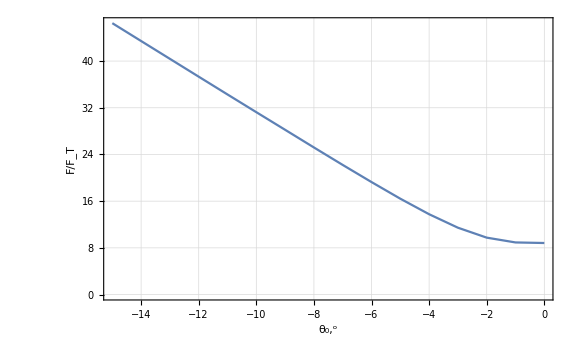

```mathematica
Flatten[{#*180/π,peregruz[# ]}]&/@Range[-15.°,0,1°];
ListPlot[%,Joined->True,FrameLabel->{"θ_0,^o","F/F_T"}]
```

# Задание 3

Функция дальности полета от начального угла входа в атмосферу

```mathematica
dist[θ0_?NumberQ]:=Module[{params,nu,neq,tk,sol},
params={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9};
nu={V[0]==√(μ/(Rz+h0)),θ[0]==θ0,r[0]==Rz+h0,s[0]==0};
neq=eq/.params;
sol=NDSolve[{eq,nu,
WhenEvent[r[t]<=Rz//.params,"StopIntegration",DetectionMethod->"Sign"]}//.params,
q,{t,0,1000}];
tk=sol[[1,1,2,0,1,1,2]];
s[t]/.sol/.t->tk//Flatten
];
```

График зависимости дальности точки приземления от начального угла входа в атмосферу θ_0 в диапазоне от минус 15 до 0 градусов

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 167.703 and t = 169.937.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 173.124 and t = 175.759.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 177.575 and t = 179.993.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

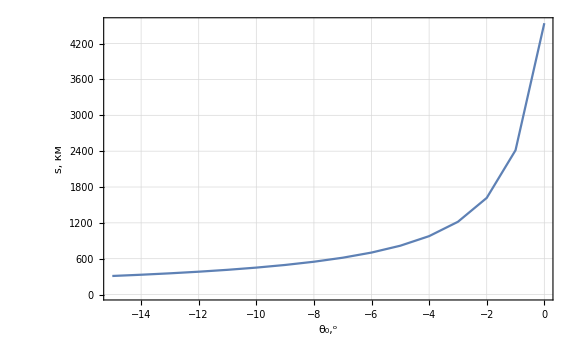

```mathematica
Flatten[{#*180/π,dist[# ]*0.001}]&/@Range[-15.°,0,1°];
ListPlot[%,Joined->True,FrameLabel->{"θ_0,^o","s, км"}]
```

## Графики траекторий спуска при θ_0 = -15° и при θ_0 = -2°

Функция возвращает список с уравнениями движения при заданном начальном угле θ_0

```mathematica
distForGraf[θ0_?NumberQ]:=Module[{params,nu,neq,tk,sol},
params={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9};
nu={V[0]==√(μ/(Rz+h0)),θ[0]==θ0,r[0]==Rz+h0,s[0]==0};
neq=eq/.params;
sol=NDSolve[{eq,nu,
WhenEvent[r[t]<=Rz//.params,"StopIntegration",DetectionMethod->"Sign"]}//.params,
q,{t,0,1000}];
tk=sol[[1,1,2,0,1,1,2]];
q/.sol
];
```

Решения для θ_0 = -15°

```mathematica
SolveFor15deg = distForGraf[-15.°]//Flatten
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 167.703 and t = 169.937.

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
r15 = SolveFor15deg[[2]];
```

```mathematica
s15 = SolveFor15deg[[4]];
```

График траектории спуска при входе в атмосферу под углом θ_0 = - 15 °

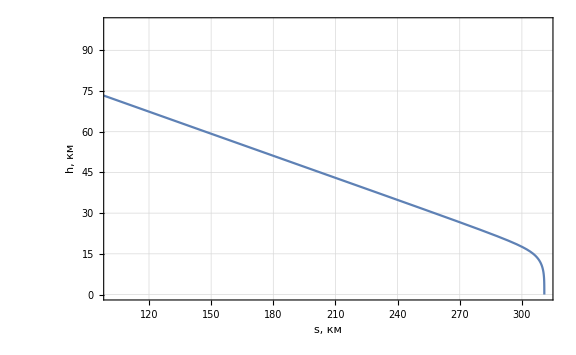

```mathematica
ParametricPlot[{s15,(r15-Rz)}*0.001/.params,{t,0,169},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio]
```

Аналогично при θ_0 = -2°

```mathematica
SolveFor2deg = distForGraf[-2.°]//Flatten
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 383.289 and t = 385.913.

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
r2 = SolveFor2deg[[2]];
```

```mathematica
s2= SolveFor2deg[[4]];
```

График траектории спуска при входе в атмосферу под углом θ_0 = - 2 °

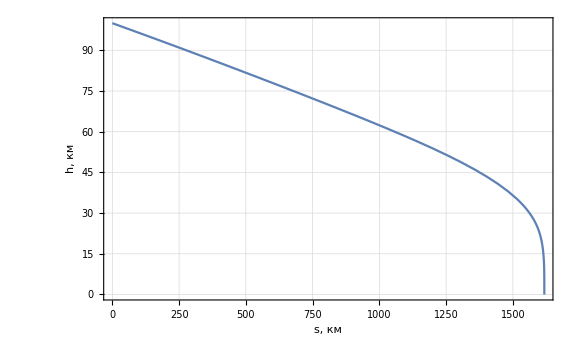

```mathematica
ParametricPlot[{s2,(r2-Rz)}*0.001/.params,{t,0,384},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio]
```